```mathematica
(*81 lines per section*)
(*r Zr-Zr C-Zr C-C Total*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/collective_PDFs"];
files={"pdf.70.4850.1_836.txt","pdf.129.4850.1_1141.txt","pdf.142.4850.1_891.txt","pdf.174.4850.1_851.txt","pdf.1126.4850.1_746.txt"};
pdfData=Table[ReadList[files[[i]],{Number,Number,Number,Number,Number}],{i,1,5}];
```

```mathematica
names={"70","129","142","174","1126"};
fullNames={"Bound-dimer","Unbound-dimer","Unbound-trimer","Bound-trimer","Bound-tetramer"};
header={"Methods","Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-Trimer","Unbound-Tetramer"};
```

```mathematica
zrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[2]]},{i,1,5}];
czr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[3]]},{i,1,5}];
cc=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]]},{i,1,5}];
tot=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[5]]},{i,1,5}];
```

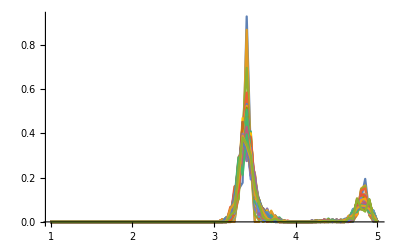

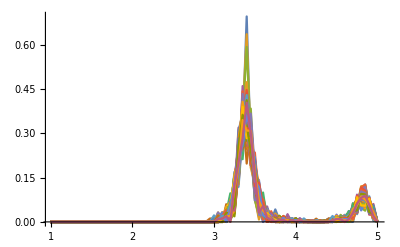

```mathematica
ListLinePlot[Partition[zrzr[[1]],81],PlotRange->All]
ListLinePlot[Partition[zrzr[[3]],81],PlotRange->All]
```

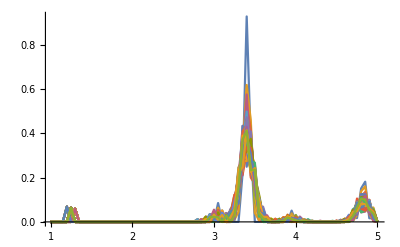
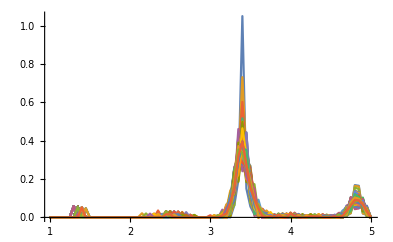
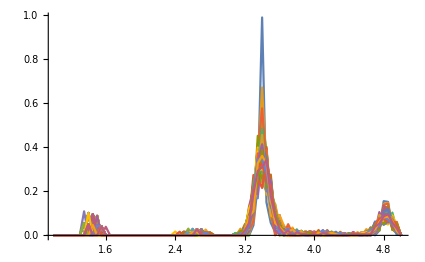
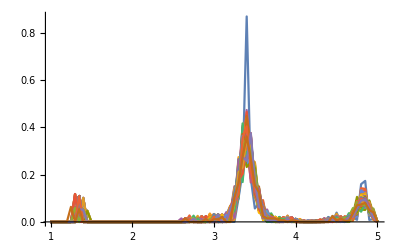
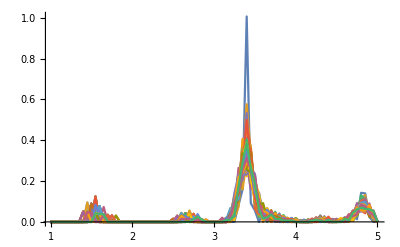

```mathematica
Table[ListLinePlot[Partition[cc[[i]],81],PlotRange->All],{i,1,5}]
```

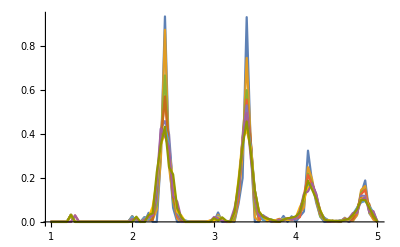

```mathematica
ListLinePlot[Partition[tot,81][[1;;10]],PlotRange->All]
```

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name,81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name,81]//Length}],15]]
```

```mathematica
With[{name=cc},ListAnimate[Table[ListLinePlot[Partition[name,81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name,81]//Length}],15]]
```

```mathematica
With[{name=zrzr},ListAnimate[Table[ListLinePlot[Partition[name,81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name,81]//Length}],15]]
```

```mathematica
Table[fullNames[[1]],{i,5}]
```

{Bound-dimer,Bound-dimer,Bound-dimer,Bound-dimer,Bound-dimer}

```mathematica
Partition[cc[[1]],81][[1;;2]]
```

{{{1.,0.},{1.05,0.},{1.1,0.},{1.15,0.},{1.2,0.},{1.25,0.0637},{1.3,0.},{1.35,0.},{1.4,0.},{1.45,0.},{1.5,0.},{1.55,0.},{1.6,0.},{1.65,0.},{1.7,0.},{1.75,0.},{1.8,0.},{1.85,0.},{1.9,0.},{1.95,0.},{2.,0.},{2.05,0.},{2.1,0.},{2.15,0.},{2.2,0.},{2.25,0.},{2.3,0.},{2.35,0.},{2.4,0.},{2.45,0.},{2.5,0.},{2.55,0.},{2.6,0.},{2.65,0.},{2.7,0.},{2.75,0.},{2.8,0.},{2.85,0.},{2.9,0.},{2.95,0.},{3.,0.},{3.05,0.0855},{3.1,0.},{3.15,0.},{3.2,0.},{3.25,0.},{3.3,0.},{3.35,0.2216},{3.4,0.9293},{3.45,0.3594},{3.5,0.},{3.55,0.},{3.6,0.},{3.65,0.},{3.7,0.},{3.75,0.},{3.8,0.},{3.85,0.},{3.9,0.},{3.95,0.051},{4.,0.},{4.05,0.},{4.1,0.},{4.15,0.},{4.2,0.},{4.25,0.},{4.3,0.},{4.35,0.},{4.4,0.},{4.45,0.},{4.5,0.},{4.55,0.},{4.6,0.},{4.65,0.},{4.7,0.018},{4.75,0.0176},{4.8,0.1511},{4.85,0.1818},{4.9,0.0166},{4.95,0.0162},{5.,0.}},{{1.,0.},{1.05,0.},{1.1,0.},{1.15,0.},{1.2,0.},{1.25,0.0637},{1.3,0.},{1.35,0.},{1.4,0.},{1.45,0.},{1.5,0.},{1.55,0.},{1.6,0.},{1.65,0.},{1.7,0.},{1.75,0.},{1.8,0.},{1.85,0.},{1.9,0.},{1.95,0.},{2.,0.},{2.05,0.},{2.1,0.},{2.15,0.},{2.2,0.},{2.25,0.},{2.3,0.},{2.35,0.},{2.4,0.},{2.45,0.},{2.5,0.},{2.55,0.},{2.6,0.},{2.65,0.},{2.7,0.},{2.75,0.},{2.8,0.},{2.85,0.},{2.9,0.},{2.95,0.},{3.,0.},{3.05,0.0642},{3.1,0.0207},{3.15,0.},{3.2,0.},{3.25,0.0094},{3.3,0.0457},{3.35,0.328},{3.4,0.6195},{3.45,0.4596},{3.5,0.0406},{3.55,0.0079},{3.6,0.},{3.65,0.},{3.7,0.},{3.75,0.},{3.8,0.},{3.85,0.},{3.9,0.},{3.95,0.0383},{4.,0.0124},{4.05,0.},{4.1,0.},{4.15,0.},{4.2,0.},{4.25,0.},{4.3,0.},{4.35,0.},{4.4,0.},{4.45,0.},{4.5,0.},{4.55,0.},{4.6,0.},{4.65,0.0138},{4.7,0.0045},{4.75,0.0309},{4.8,0.1382},{4.85,0.1607},{4.9,0.0373},{4.95,0.0041},{5.,0.}}}

```mathematica
trainSet=Table[Table[{Partition[cc[[i]],81][[j]]->ToString@fullNames[[i]]},{j,1,2}],{i,1,5}];
```

```mathematica
Table[Table[Partition[cc[[i]],81][[j]]->fullNames[[i]],{j,1,2}],{i,1,5}][[1]][[1]]
```

{{1.,0.},{1.05,0.},{1.1,0.},{1.15,0.},{1.2,0.},{1.25,0.0637},{1.3,0.},{1.35,0.},{1.4,0.},{1.45,0.},{1.5,0.},{1.55,0.},{1.6,0.},{1.65,0.},{1.7,0.},{1.75,0.},{1.8,0.},{1.85,0.},{1.9,0.},{1.95,0.},{2.,0.},{2.05,0.},{2.1,0.},{2.15,0.},{2.2,0.},{2.25,0.},{2.3,0.},{2.35,0.},{2.4,0.},{2.45,0.},{2.5,0.},{2.55,0.},{2.6,0.},{2.65,0.},{2.7,0.},{2.75,0.},{2.8,0.},{2.85,0.},{2.9,0.},{2.95,0.},{3.,0.},{3.05,0.0855},{3.1,0.},{3.15,0.},{3.2,0.},{3.25,0.},{3.3,0.},{3.35,0.2216},{3.4,0.9293},{3.45,0.3594},{3.5,0.},{3.55,0.},{3.6,0.},{3.65,0.},{3.7,0.},{3.75,0.},{3.8,0.},{3.85,0.},{3.9,0.},{3.95,0.051},{4.,0.},{4.05,0.},{4.1,0.},{4.15,0.},{4.2,0.},{4.25,0.},{4.3,0.},{4.35,0.},{4.4,0.},{4.45,0.},{4.5,0.},{4.55,0.},{4.6,0.},{4.65,0.},{4.7,0.018},{4.75,0.0176},{4.8,0.1511},{4.85,0.1818},{4.9,0.0166},{4.95,0.0162},{5.,0.}}→Bound-dimer

```mathematica
results=With[{trainSize=5,valSize=100},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,2}];
c=Classify[trainSet];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,2}],{timeStep,trainSize,trainSize+valSize}]//TableForm];
```

```mathematica
(*results for 1 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,2}];
accuracy//TableForm
```

Bound-dimer | 0.0792079
Unbound-dimer | 0.980198

```mathematica
(*results for 2 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,2}];
accuracy//TableForm
```

Bound-dimer | 0.168317
Unbound-dimer | 1.

```mathematica
(*results for 5 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,2}];
accuracy//TableForm
```

Bound-dimer | 0.891089
Unbound-dimer | 1.

```mathematica
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,2}];
accuracy//TableForm
```

Bound-dimer | 0.970297
Unbound-dimer | 1.

```mathematica
Intersection[Transpose[results[[1]]][[1]],Transpose[results[[1]]][[2]]]
```

{Unbound-dimer}

```mathematica
Options
```

Options

```mathematica
Options@Classify
```

{Method→Automatic,PerformanceGoal→Automatic,NominalVariables→Automatic,ValidationSet→None,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,Weights→Automatic,FeatureWeights→Automatic,DistributionPostProcessing→Automatic,PredictionName→Automatic,RecordLog→True,FeatureExtractor→None,ImputeMissingValues→True,ProcessorCaching→True,BatchProcessing→Automatic,MinimalPreprocessing→False,ClassPriors→Automatic,TieBreakerFunction→RandomChoice}

```mathematica
results=With[{trainSize=5,valSize=100},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,2}];
c=Classify[trainSet,Method->"SupportVectorMachine"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,2}],{timeStep,trainSize,trainSize+valSize}]//TableForm];
```

```mathematica
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,2}];
accuracy//TableForm
```

Bound-dimer | 0.851485
Unbound-dimer | 0.990099

```mathematica
results=With[{trainSize=5,valSize=100,method="NearestNeighbors"},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,2}];
c=Classify[trainSet,Method->method];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,2}],{timeStep,trainSize,trainSize+valSize}]//TableForm];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,2}];
accuracy//TableForm
```

Bound-dimer | 0.871287
Unbound-dimer | 0.960396

```mathematica
methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
```

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

```mathematica
Table[results=With[{trainSize=5,valSize=100,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,2}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,2}],{timeStep,trainSize,trainSize+valSize}]//TableForm];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,2}];
accuracy//TableForm,{i,1,5}]
```

{Bound-dimer | 0.891089
Unbound-dimer | 1.,Bound-dimer | 0.851485
Unbound-dimer | 0.673267,Bound-dimer | 0.990099
Unbound-dimer | 0.980198,Bound-dimer | 0.871287
Unbound-dimer | 0.960396,Bound-dimer | 0.673267
Unbound-dimer | 0.80198}

```mathematica
Table[results=With[{maxTypes=3,trainSize=5,valSize=100,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]//TableForm];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,3}];
Transpose@accuracy//TableForm,{i,1,5}]//TableForm
```

Bound-dimer | Unbound-dimer | Unbound-trimer
0.950495 | 0.930693 | 0.663366
Bound-dimer | Unbound-dimer | Unbound-trimer
0.673267 | 0.455446 | 0.376238
Bound-dimer | Unbound-dimer | Unbound-trimer
1. | 0.891089 | 0.831683
Bound-dimer | Unbound-dimer | Unbound-trimer
1. | 0.782178 | 0.257426
Bound-dimer | Unbound-dimer | Unbound-trimer
0.970297 | 0.821782 | 0.574257

```mathematica
Table[results=With[{maxTypes=3,trainSize=10,valSize=100,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]//TableForm];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results[[1]]][[type]],Transpose[results[[1]]][[type]][[1]]]/Length[Transpose[results[[1]]][[type]]]//N},{type,1,3}];
Transpose@accuracy//TableForm,{i,1,5}]//TableForm
```

Bound-dimer | Unbound-dimer | Unbound-trimer
1. | 0.831683 | 0.970297
Bound-dimer | Unbound-dimer | Unbound-trimer
0.623762 | 0.60396 | 0.435644
Bound-dimer | Unbound-dimer | Unbound-trimer
0.970297 | 0.90099 | 0.910891
Bound-dimer | Unbound-dimer | Unbound-trimer
1. | 0.0792079 | 0.70297
Bound-dimer | Unbound-dimer | Unbound-trimer
0.851485 | 0.950495 | 0.623762

```mathematica
Table[Partition[cc[[i]],81]//Length,{i,1,5}]
```

{168,229,179,171,150}

```mathematica
scores=With[{maxTypes=3},Table[results=With[{trainSize=100,valSize=68,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResults=Join[{header[[1;;4]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,6}]];
```

1. | 0.990099 | 0.980198
0.752475 | 0.80198 | 0.742574
1. | 0.950495 | 0.980198
1. | 0.990099 | 0.920792
1. | 1. | 0.970297
1. | 1. | 0.980198

```mathematica
(*trainingSet=50,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer
LogisticRegression | 1. | 0.990099 | 0.980198
Markov | 0.752475 | 0.80198 | 0.742574
NaiveBayes | 1. | 0.950495 | 0.980198
NearestNeighbors | 1. | 0.990099 | 0.920792
RandomForest | 1. | 1. | 0.970297
SupportVectorMachine | 1. | 1. | 0.980198

```mathematica
(*trainingSet=10,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer
LogisticRegression | 1. | 0.831683 | 0.970297
Markov | 0.623762 | 0.60396 | 0.435644
NaiveBayes | 0.970297 | 0.90099 | 0.910891
NearestNeighbors | 1. | 0.0792079 | 0.70297
RandomForest | 0.821782 | 0.831683 | 0.80198
SupportVectorMachine | 0.752475 | 0.851485 | 0.861386

```mathematica
(*trainingSet=5,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer
LogisticRegression | 0.950495 | 0.930693 | 0.663366
Markov | 0.673267 | 0.455446 | 0.376238
NaiveBayes | 1. | 0.891089 | 0.831683
NearestNeighbors | 1. | 0.782178 | 0.257426
RandomForest | 0.970297 | 0.881188 | 0.574257
SupportVectorMachine | 0.861386 | 0.960396 | 0.534653

```mathematica
(*trainingSet=5,ValidationSet=10*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer
LogisticRegression | 1. | 0.952381 | 0.714286
Markov | 0.666667 | 0.285714 | 0.380952
NaiveBayes | 1. | 0.857143 | 0.714286
NearestNeighbors | 1. | 0.714286 | 0.333333
RandomForest | 1. | 0.904762 | 0.619048
SupportVectorMachine | 0.904762 | 1. | 0.571429